# Code for generating the results in Table I

```mathematica
SeedRandom[1234];
```

### Generating Random test points (commented by default)

Here we can generate as many testing points as we want. 

NOTE: the high-fidelity solution has convergence issues for negative q. Proper seeding can solve these problems, but it is recommended to compare the methods in the region q>0.

### Initializing global parameters:

```mathematica
Xmin=-10;                                    (* Lower limit range for the function *)
Xmax=10;                                      (* Upper limit range for the function *)
dx=0.02;                                       (*Step size for the finite element method*)
x=Range[Xmin,Xmax,dx]; (*Initialize the abcissa*)
len=Length[x];     (*Initialize the lengeth of solution vector*)

(*Laplacian matrix for the discrete system*)
lap=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{len,len}]/dx^2;
```

### Variable initialization:

#### Placeholders for the high-fidelity solution of the differential equation

```mathematica
phi=Array[phiVal,len];(* Placeholder for a particular eigenfunction we are calculating *)
psi=Array[phiVal,len];(* Placeholder for a particular dual function we are calculating *)
lam;(* Placeholder for a particular eigenvalue we are calculating *)
```

### Eigenvalue Problem definition:

We are interested in solving for the stationary states of the Gross-Pitaevskii equation in 1 dimension with a harmonic potential:

```mathematica
Falpha[q_,k_,PHI_,Lam_]:=(Dot[-lap,PHI]+k*(x^2)*PHI+q*PHI^3-Lam*PHI);
```

```mathematica
q0=5; (*Example Nonlinear coupling for the Gross–Pitaevskii equation*)
k0=0.5;      (*Example Coupling constant for the harmonic potential*)

eigEq[q_,k_]:=(Dot[-lap,phi]+k*(x^2)*phi+q*phi^3==lam*phi);(*Eigenvalue equation*)
normEq[q_,k_]:=Dot[phi,phi]==1.0/dx;(*Normalization condition*)

eqns[q_,k_]:=Append[Thread[eigEq[q,k]],normEq[q,k]]; (*Full (N+1) equation set*)
```

### Finding the (High-Fidelity) lowest energy solution:

We utilize FindRoot to find the solution to the eigenvalue equation. We use an eigenfunction of the harmonic oscillator, or a constant function, as an initial guess to speed up calculations. FindRoot helps us to bypass finding all of the other eigenfunctions we don’t care about by starting near the basin of attraction of the first eigenmode.

```mathematica
sol[q_,k_]:=FindRoot[eqns[q,k],Transpose[{Prepend[phi,lam],Prepend[Exp[-x^2*Sqrt[k]/2]/(Pi/Sqrt[k])^(1/4),Sqrt[k]]}],PrecisionGoal->10]; (*Solution routine for the full set of (N+1) equations, as a function of q and k*)
```

```mathematica
solGuess[q_,k_,Guess_]:=FindRoot[eqns[q,k],Transpose[{Prepend[phi,lam],Flatten[Guess]}],PrecisionGoal->10]; (*Same routine, but allows for a user-defined guess*)
```

## Constructing the modular function that gives results for a given basis

```mathematica
ResultsCalculator[Basis_]:=Module[{timeMCMC},
listPhi=Basis;
numTrain=Length[listPhi];

listCoeff=Array[aTest,numTrain];(*Coefficients of the RB solution*)
RBlam; (*Placeholder for the approximate eigenvalue*)

RBphi=Dot[listCoeff,listPhi];(*Initialized ansatz function for the RB approximation*)
qRB; kRB; (*Declare the variables q and k for the RB method*)
RBeigLHS=Dot[listPhi,(Dot[-lap,RBphi]+kRB*(x^2)*RBphi+qRB*Times[Times[RBphi,RBphi],RBphi]-RBlam*RBphi)];(*Eigenvalue equation*)
RBnormLHS=Dot[RBphi,RBphi]-1.0/dx;(*Normalization condition*)

(*We initialize an array of equations, since Mathematica struggles with the vector notation*)
RBeqns={};
AppendTo[RBeqns,(Expand[RBnormLHS]==0)];
For[eqIndex=1,eqIndex<=numTrain,eqIndex++,
AppendTo[RBeqns,(Expand[RBeigLHS[[eqIndex]]]==0)];(*The Expand function is important to limit the overhead of FindRoot*)
];

RBvars=Append[listCoeff,RBlam]; (*List of variables, the linear combination coefficient, plus the eigenvalue*)

(*Initialize a seed for FindRoot*)

Guess=Join[{1},ConstantArray[0,numTrain-1]];
AppendTo[Guess,1];
seedRB=Transpose[{RBvars,Guess}];

solRB[q_,k_]:=FindRoot[RBeqns/.{qRB->q,kRB->k},seedRB,PrecisionGoal->10]; 
(*Solution routine for the reduced set of equations, as a function of q and k*)



solRBGuess[q_,k_,Guess_]:=FindRoot[RBeqns/.{qRB->q,kRB->k},Transpose[{RBvars,Flatten[Guess]}],PrecisionGoal->10];(*Same routine, but allows for a user-defined guess*)
numTest=Length[TestingPoints];
RBresults=ConstantArray[0.,numTest];
(*Declare an array of solution coefficients*)
RBcoeffResults=ConstantArray[0.,{numTest,numTrain}];

timeMCMC=Timing[
For[indexTest=1,indexTest<=numTest,indexTest++,
s=solRB[TestingPoints[[indexTest]][[1]],TestingPoints[[indexTest]][[2]]];
RBresults[[indexTest]]=RBlam/.s;(*Testing points are indexed by q and k, in that order*)
RBcoeffResults[[indexTest]]=listCoeff/.s;
]];

ERROR=(RBresults-HFresults);(*Absolute approximation error*)
relERROR=ERROR/HFresults;
RMSE=Norm[relERROR]/Sqrt[numTest];
{timeMCMC[[1]],RMSE}



]
```

```mathematica
FalphaCalculator[Basis_,TestPointsLH_]:=Module[{timeMCMC},
listPhi=Basis;
numTrain=Length[listPhi];

listCoeff=Array[aTest,numTrain];(*Coefficients of the RB solution*)
RBlam; (*Placeholder for the approximate eigenvalue*)

RBphi=Dot[listCoeff,listPhi];(*Initialized ansatz function for the RB approximation*)
qRB; kRB; (*Declare the variables q and k for the RB method*)
RBeigLHS=Dot[listPhi,(Dot[-lap,RBphi]+kRB*(x^2)*RBphi+qRB*Times[Times[RBphi,RBphi],RBphi]-RBlam*RBphi)];(*Eigenvalue equation*)
RBnormLHS=Dot[RBphi,RBphi]-1.0/dx;(*Normalization condition*)

(*We initialize an array of equations, since Mathematica struggles with the vector notation*)
RBeqns={};
AppendTo[RBeqns,(Expand[RBnormLHS]==0)];
For[eqIndex=1,eqIndex<=numTrain,eqIndex++,
AppendTo[RBeqns,(Expand[RBeigLHS[[eqIndex]]]==0)];(*The Expand function is important to limit the overhead of FindRoot*)
];

RBvars=Append[listCoeff,RBlam]; (*List of variables, the linear combination coefficient, plus the eigenvalue*)

(*Initialize a seed for FindRoot*)

Guess=Join[{1},ConstantArray[0,numTrain-1]];
AppendTo[Guess,1];
seedRB=Transpose[{RBvars,Guess}];

solRB[q_,k_]:=FindRoot[RBeqns/.{qRB->q,kRB->k},seedRB,PrecisionGoal->10]; 
(*Solution routine for the reduced set of equations, as a function of q and k*)



solRBGuess[q_,k_,Guess_]:=FindRoot[RBeqns/.{qRB->q,kRB->k},Transpose[{RBvars,Flatten[Guess]}],PrecisionGoal->10];(*Same routine, but allows for a user-defined guess*)
numTest=Length[TestPointsLH];
RBresults=ConstantArray[0.,numTest];
(*Declare an array of solution coefficients*)
RBcoeffResults=ConstantArray[0.,{numTest,numTrain}];
FalpList={};
timeMCMC=Timing[
For[indexTest=1,indexTest<=numTest,indexTest++,
s=solRB[TestPointsLH[[indexTest]][[1]],TestPointsLH[[indexTest]][[2]]];
AppendTo[FalpList,{dx*Norm[Falpha[TestPointsLH[[indexTest]][[1]],TestPointsLH[[indexTest]][[2]],

RBphi/.s,RBlam/.s]],

TestPointsLH[[indexTest]]}];

]];

(*FalpList*)
FalpList

]
```

```mathematica
BasisConstruction[TrainPoints_]:=Module[{},


numTrain=Length[TrainPoints];
listPhi=Array[trainPhi,{numTrain,len}]; (*List of the training functions 'phi'*)

For[i=1,i≤numTrain,i++,
placeholderSol=sol[TrainPoints[[i]][[1]],TrainPoints[[i]][[2]]];(*dummy variable for substitution*)
listPhi[[i]]=phi/.placeholderSol;

];

listPhi

]
```

```mathematica
LHCMatrixRandomizer[nmax_]:=Module[{},

TrainingNumberHL=nmax;
MatrixLHIn=Table[i,{i,1,TrainingNumberHL},{j,1,2}];
For[i=1,i<=TrainingNumberHL,i++,

Indexval=RandomInteger[{1,TrainingNumberHL}];
MatVal1=MatrixLHIn[[i]][[2]];
MatVal2=MatrixLHIn[[Indexval]][[2]];
MatrixLHIn[[i]][[2]]=MatVal2;
MatrixLHIn[[Indexval]][[2]]=MatVal1


];
MatrixLHIn
]
```

```mathematica
KLimits={5,30};
QLimits={0,30};
```

```mathematica
TraininPointsMakerTrain[Matrixlh_]:=Module[{},
TrainingNumberHL=Length[Matrixlh];
TP={};

TotalPoints=TrainingNumberHL;
For[ik=1,ik<=TotalPoints,ik++,


AppendTo[TP,{(Matrixlh[[ik]][[1]])*(QLimits[[2]]-QLimits[[1]])/(TrainingNumberHL+1)+QLimits[[1]],(Matrixlh[[ik]][[2]])*(KLimits[[2]]-KLimits[[1]])/(TrainingNumberHL+1)+KLimits[[1]]}]




];

TP
]
```

```mathematica
SVDCreator[Basis_,NMax_]:=Module[{},
{u, σ, v} = SingularValueDecomposition[listPhi,NMax];
Transpose[v][[1;;NMax]]*1/Sqrt[dx]


]
```

```mathematica
MatrixTesting=LHCMatrixRandomizer[500]
```

{{1,198},{2,111},{3,337},{4,113},{5,37},{6,387},{7,45},{8,96},{9,57},{10,116},{11,401},{12,195},{13,176},{14,136},{15,235},{16,206},{17,280},{18,1},{19,170},{20,225},{21,486},{22,292},{23,259},{24,77},{25,33},{26,323},{27,394},{28,438},{29,267},{30,93},{31,200},{32,192},{33,65},{34,180},{35,50},{36,303},{37,246},{38,131},{39,361},{40,174},{41,242},{42,249},{43,316},{44,279},{45,491},{46,208},{47,151},{48,342},{49,55},{50,416},{51,428},{52,211},{53,310},{54,354},{55,315},{56,137},{57,307},{58,60},{59,398},{60,84},{61,243},{62,8},{63,487},{64,223},{65,485},{66,286},{67,194},{68,344},{69,177},{70,149},{71,24},{72,227},{73,448},{74,105},{75,236},{76,126},{77,420},{78,499},{79,444},{80,202},{81,348},{82,322},{83,118},{84,128},{85,495},{86,439},{87,254},{88,294},{89,94},{90,44},{91,465},{92,377},{93,216},{94,12},{95,482},{96,129},{97,239},{98,147},{99,484},{100,431},{101,281},{102,119},{103,261},{104,102},{105,159},{106,181},{107,95},{108,182},{109,101},{110,436},{111,76},{112,167},{113,173},{114,459},{115,14},{116,59},{117,371},{118,189},{119,460},{120,278},{121,168},{122,196},{123,435},{124,422},{125,75},{126,124},{127,300},{128,410},{129,301},{130,467},{131,228},{132,4},{133,347},{134,43},{135,62},{136,295},{137,392},{138,40},{139,319},{140,430},{141,240},{142,427},{143,193},{144,127},{145,346},{146,92},{147,30},{148,273},{149,500},{150,204},{151,53},{152,107},{153,232},{154,99},{155,256},{156,47},{157,269},{158,476},{159,475},{160,336},{161,39},{162,221},{163,373},{164,492},{165,470},{166,74},{167,172},{168,245},{169,71},{170,153},{171,64},{172,262},{173,201},{174,283},{175,22},{176,31},{177,140},{178,417},{179,426},{180,141},{181,357},{182,349},{183,481},{184,318},{185,419},{186,328},{187,109},{188,478},{189,163},{190,270},{191,356},{192,453},{193,333},{194,28},{195,366},{196,415},{197,233},{198,446},{199,81},{200,120},{201,21},{202,130},{203,78},{204,432},{205,144},{206,391},{207,85},{208,285},{209,409},{210,367},{211,199},{212,380},{213,197},{214,72},{215,220},{216,66},{217,343},{218,257},{219,362},{220,98},{221,374},{222,287},{223,212},{224,472},{225,203},{226,61},{227,150},{228,345},{229,115},{230,306},{231,219},{232,67},{233,332},{234,418},{235,247},{236,304},{237,389},{238,471},{239,241},{240,82},{241,396},{242,450},{243,477},{244,185},{245,277},{246,237},{247,331},{248,36},{249,457},{250,263},{251,378},{252,255},{253,87},{254,429},{255,134},{256,360},{257,402},{258,498},{259,314},{260,405},{261,370},{262,56},{263,399},{264,83},{265,80},{266,423},{267,34},{268,358},{269,86},{270,455},{271,313},{272,23},{273,406},{274,209},{275,299},{276,266},{277,353},{278,90},{279,231},{280,133},{281,69},{282,480},{283,379},{284,463},{285,154},{286,268},{287,451},{288,325},{289,305},{290,440},{291,27},{292,264},{293,35},{294,186},{295,382},{296,51},{297,156},{298,253},{299,161},{300,29},{301,258},{302,329},{303,352},{304,445},{305,489},{306,146},{307,175},{308,302},{309,368},{310,106},{311,412},{312,400},{313,335},{314,251},{315,152},{316,397},{317,458},{318,290},{319,355},{320,15},{321,289},{322,26},{323,52},{324,274},{325,442},{326,104},{327,162},{328,320},{329,148},{330,447},{331,293},{332,215},{333,414},{334,390},{335,164},{336,187},{337,461},{338,224},{339,272},{340,424},{341,91},{342,190},{343,338},{344,456},{345,291},{346,58},{347,178},{348,73},{349,222},{350,276},{351,408},{352,403},{353,350},{354,49},{355,18},{356,383},{357,421},{358,79},{359,179},{360,385},{361,388},{362,308},{363,188},{364,376},{365,443},{366,2},{367,275},{368,441},{369,229},{370,469},{371,312},{372,340},{373,88},{374,210},{375,32},{376,488},{377,234},{378,404},{379,411},{380,497},{381,42},{382,121},{383,100},{384,184},{385,296},{386,7},{387,365},{388,68},{389,145},{390,205},{391,41},{392,46},{393,271},{394,38},{395,171},{396,317},{397,103},{398,244},{399,330},{400,20},{401,213},{402,252},{403,97},{404,393},{405,298},{406,135},{407,108},{408,139},{409,433},{410,138},{411,6},{412,288},{413,13},{414,3},{415,384},{416,191},{417,363},{418,452},{419,326},{420,483},{421,217},{422,248},{423,110},{424,112},{425,238},{426,466},{427,341},{428,395},{429,122},{430,260},{431,70},{432,54},{433,462},{434,155},{435,117},{436,425},{437,468},{438,324},{439,207},{440,9},{441,311},{442,369},{443,327},{444,413},{445,250},{446,449},{447,479},{448,218},{449,10},{450,48},{451,364},{452,165},{453,381},{454,226},{455,407},{456,166},{457,284},{458,372},{459,339},{460,386},{461,158},{462,473},{463,464},{464,16},{465,214},{466,454},{467,351},{468,183},{469,434},{470,493},{471,123},{472,490},{473,282},{474,132},{475,63},{476,359},{477,321},{478,19},{479,169},{480,496},{481,25},{482,334},{483,143},{484,157},{485,230},{486,265},{487,114},{488,494},{489,5},{490,89},{491,160},{492,375},{493,474},{494,17},{495,11},{496,297},{497,142},{498,309},{499,125},{500,437}}

```mathematica
TestingPoints=N[TraininPointsMakerTrain[LHCMatrixRandomizer[500]]]
```

{{0.0598802,10.2894},{0.11976,8.84232},{0.179641,8.64271},{0.239521,21.1677},{0.299401,6.29741},{0.359281,14.8802},{0.419162,11.2375},{0.479042,24.1118},{0.538922,18.024},{0.598802,16.3772},{0.658683,14.4311},{0.718563,13.982},{0.778443,20.4691},{0.838323,17.2255},{0.898204,6.74651},{0.958084,15.0299},{1.01796,11.3373},{1.07784,19.5709},{1.13772,10.5389},{1.1976,17.8743},{1.25749,24.0619},{1.31737,6.64671},{1.37725,12.984},{1.43713,8.39321},{1.49701,27.2555},{1.55689,10.8882},{1.61677,27.505},{1.67665,10.7385},{1.73653,23.6627},{1.79641,17.7745},{1.85629,7.84431},{1.91617,26.7066},{1.97605,21.4172},{2.03593,18.9222},{2.09581,15.1796},{2.15569,10.3393},{2.21557,28.4032},{2.27545,8.34331},{2.33533,5.3992},{2.39521,18.5729},{2.45509,22.8643},{2.51497,16.1776},{2.57485,22.7645},{2.63473,16.0778},{2.69461,7.39521},{2.75449,11.986},{2.81437,28.3533},{2.87425,29.9501},{2.93413,6.49701},{2.99401,17.9242},{3.05389,19.6707},{3.11377,19.0719},{3.17365,13.5828},{3.23353,9.89022},{3.29341,8.59281},{3.35329,23.8124},{3.41317,7.94411},{3.47305,28.3034},{3.53293,16.477},{3.59281,27.5549},{3.65269,17.6747},{3.71257,17.4251},{3.77246,17.2754},{3.83234,15.3792},{3.89222,9.04192},{3.9521,8.94212},{4.01198,10.6886},{4.07186,16.3273},{4.13174,11.3872},{4.19162,8.09381},{4.2515,24.9601},{4.31138,26.6567},{4.37126,29.1018},{4.43114,16.2774},{4.49102,5.3493},{4.5509,16.9261},{4.61078,19.1218},{4.67066,20.6687},{4.73054,28.8523},{4.79042,12.6347},{4.8503,22.6148},{4.91018,29.7006},{4.97006,23.2635},{5.02994,23.1138},{5.08982,23.014},{5.1497,13.483},{5.20958,15.8782},{5.26946,26.008},{5.32934,13.0838},{5.38922,27.3553},{5.4491,13.9321},{5.50898,18.2236},{5.56886,8.24351},{5.62874,8.04391},{5.68862,23.7126},{5.7485,7.34531},{5.80838,13.3333},{5.86826,29.3513},{5.92814,11.6866},{5.98802,23.9621},{6.0479,20.02},{6.10778,14.7305},{6.16766,14.98},{6.22754,26.8563},{6.28743,16.5269},{6.34731,20.519},{6.40719,28.7026},{6.46707,20.7186},{6.52695,6.0479},{6.58683,24.2615},{6.64671,18.2735},{6.70659,25.4092},{6.76647,7.89421},{6.82635,25.4591},{6.88623,13.8323},{6.94611,12.4351},{7.00599,12.6846},{7.06587,24.2116},{7.12575,23.4631},{7.18563,5.0998},{7.24551,6.1477},{7.30539,11.487},{7.36527,16.8263},{7.42515,21.4671},{7.48503,5.7984},{7.54491,5.1996},{7.60479,19.521},{7.66467,18.8224},{7.72455,19.3713},{7.78443,21.6667},{7.84431,11.0878},{7.90419,6.59681},{7.96407,10.6387},{8.02395,11.5868},{8.08383,24.1617},{8.14371,13.0339},{8.20359,24.8104},{8.26347,14.3313},{8.32335,24.7605},{8.38323,15.6786},{8.44311,29.0519},{8.50299,19.8703},{8.56287,18.7226},{8.62275,25.8583},{8.68263,12.7844},{8.74251,17.525},{8.8024,20.9182},{8.86228,20.9681},{8.92216,26.1078},{8.98204,7.64471},{9.04192,16.8762},{9.1018,13.8822},{9.16168,19.7705},{9.22156,26.7565},{9.28144,12.0858},{9.34132,14.7804},{9.4012,14.2315},{9.46108,25.5589},{9.52096,9.39122},{9.58084,28.2036},{9.64072,18.6228},{9.7006,22.7146},{9.76048,14.9301},{9.82036,10.988},{9.88024,28.0539},{9.94012,27.4052},{10.,28.9521},{10.0599,18.4731},{10.1198,6.0978},{10.1796,21.7166},{10.2395,6.34731},{10.2994,24.5609},{10.3593,11.8862},{10.4192,14.1317},{10.479,17.475},{10.5389,7.44511},{10.5988,24.8603},{10.6587,14.8303},{10.7186,10.7884},{10.7784,23.3633},{10.8383,18.1238},{10.8982,12.1856},{10.9581,12.5349},{11.018,5.5489},{11.0778,25.1597},{11.1377,15.6287},{11.1976,18.1737},{11.2575,13.3832},{11.3174,21.018},{11.3772,17.3752},{11.4371,29.2016},{11.497,21.9162},{11.5569,27.4551},{11.6168,11.7864},{11.6766,21.7665},{11.7365,14.3812},{11.7964,26.507},{11.8563,14.6307},{11.9162,17.1756},{11.976,18.9721},{12.0359,26.3573},{12.0958,16.6766},{12.1557,18.6727},{12.2156,13.4331},{12.2754,22.515},{12.3353,22.9142},{12.3952,22.3154},{12.4551,25.3094},{12.515,11.2874},{12.5749,17.9741},{12.6347,18.3234},{12.6946,9.84032},{12.7545,13.7824},{12.8144,24.4112},{12.8743,8.44311},{12.9341,22.016},{12.994,15.5788},{13.0539,21.3174},{13.1138,17.6248},{13.1737,22.2156},{13.2335,29.6507},{13.2934,12.8343},{13.3533,26.1577},{13.4132,23.1637},{13.4731,17.3253},{13.5329,8.79242},{13.5928,17.1257},{13.6527,29.4012},{13.7126,7.69461},{13.7725,27.1557},{13.8323,9.59082},{13.8922,7.29541},{13.9521,26.2575},{14.012,18.4232},{14.0719,6.44711},{14.1317,28.1537},{14.1916,15.2295},{14.2515,11.1876},{14.3114,16.976},{14.3713,5.2495},{14.4311,10.0898},{14.491,17.0758},{14.5509,24.7106},{14.6108,6.39721},{14.6707,27.6048},{14.7305,23.5629},{14.7904,29.8503},{14.8503,26.4571},{14.9102,23.2136},{14.9701,20.8683},{15.0299,8.49301},{15.0898,17.0259},{15.1497,19.3214},{15.2096,20.3693},{15.2695,29.501},{15.3293,5.9481},{15.3892,25.0599},{15.4491,5.0499},{15.509,26.0579},{15.5689,11.0379},{15.6287,10.2395},{15.6886,6.69661},{15.7485,7.54491},{15.8084,29.9002},{15.8683,27.9042},{15.9281,27.8543},{15.988,18.7725},{16.0479,16.0279},{16.1078,19.4711},{16.1677,25.8084},{16.2275,8.29341},{16.2874,22.1158},{16.3473,28.4531},{16.4072,21.2176},{16.4671,29.1517},{16.5269,6.89621},{16.5868,20.7685},{16.6467,25.01},{16.7066,24.6108},{16.7665,22.0659},{16.8263,18.8723},{16.8862,26.5569},{16.9461,15.7285},{17.006,8.74251},{17.0659,9.49102},{17.1257,6.94611},{17.1856,5.8982},{17.2455,28.5529},{17.3054,20.1697},{17.3653,20.4192},{17.4251,21.8663},{17.485,23.7625},{17.5449,5.5988},{17.6048,13.2834},{17.6647,6.54691},{17.7246,27.7046},{17.7844,24.012},{17.8443,12.8842},{17.9042,27.006},{17.9641,6.84631},{18.024,7.04591},{18.0838,19.2715},{18.1437,5.4491},{18.2036,10.489},{18.2635,26.9062},{18.3234,22.4651},{18.3832,14.481},{18.4431,10.4391},{18.503,24.3613},{18.5629,5.499},{18.6228,15.479},{18.6826,8.99202},{18.7425,7.19561},{18.8024,14.1816},{18.8623,24.6607},{18.9222,24.3114},{18.982,15.4291},{19.0419,23.6128},{19.1018,28.503},{19.1617,26.8064},{19.2216,21.517},{19.2814,10.1896},{19.3413,12.1357},{19.4012,5.998},{19.4611,9.69062},{19.521,13.5329},{19.5808,11.6367},{19.6407,21.3673},{19.7006,6.99601},{19.7605,24.4611},{19.8204,21.6168},{19.8802,16.1277},{19.9401,12.0359},{20.,23.0639},{20.0599,12.7345},{20.1198,20.8184},{20.1796,21.9661},{20.2395,25.9082},{20.2994,15.0798},{20.3593,22.3653},{20.4192,24.9102},{20.479,22.2655},{20.5389,15.5289},{20.5988,11.9361},{20.6587,14.0319},{20.7186,7.49501},{20.7784,7.59481},{20.8383,8.14371},{20.8982,9.09182},{20.9581,20.2695},{21.018,27.9541},{21.0778,29.6008},{21.1377,19.8204},{21.1976,27.7545},{21.2575,13.7325},{21.3174,29.5509},{21.3772,23.4132},{21.4371,15.978},{21.497,5.2994},{21.5569,19.022},{21.6168,7.74451},{21.6766,13.6826},{21.7365,15.9281},{21.7964,11.1377},{21.8563,12.5848},{21.9162,9.74052},{21.976,5.8483},{22.0359,26.4072},{22.0958,19.2216},{22.1557,16.7764},{22.2156,14.5808},{22.2754,22.1657},{22.3353,18.0739},{22.3952,15.2794},{22.4551,9.94012},{22.515,14.5309},{22.5749,28.9022},{22.6347,27.2056},{22.6946,10.8383},{22.7545,14.0818},{22.8144,7.09581},{22.8743,16.7265},{22.9341,12.9341},{22.994,18.523},{23.0539,9.24152},{23.1138,28.1038},{23.1737,10.3892},{23.2335,21.2675},{23.2934,22.6647},{23.3533,12.2355},{23.4132,29.4511},{23.4731,12.3852},{23.5329,10.0399},{23.5928,13.1337},{23.6527,29.8004},{23.7126,23.513},{23.7725,25.6088},{23.8323,9.19162},{23.8922,13.6327},{23.9521,16.2275},{24.012,5.1497},{24.0719,20.2196},{24.1317,22.4152},{24.1916,27.8044},{24.2515,25.509},{24.3114,19.9202},{24.3713,14.2814},{24.4311,5.6986},{24.491,26.3074},{24.5509,25.7585},{24.6108,8.69261},{24.6707,27.6547},{24.7305,9.14172},{24.7904,6.1976},{24.8503,23.8623},{24.9102,13.1836},{24.9701,18.3733},{25.0299,26.9561},{25.0898,19.9701},{25.1497,16.5768},{25.2096,15.8283},{25.2695,5.7485},{25.3293,9.44112},{25.3892,20.3194},{25.4491,26.2076},{25.509,9.99002},{25.5689,28.004},{25.6287,11.5369},{25.6886,21.5669},{25.7485,17.8244},{25.8084,28.6527},{25.8683,20.6188},{25.9281,19.6208},{25.988,8.89222},{26.0479,29.7505},{26.1078,29.3014},{26.1677,9.54092},{26.2275,10.5888},{26.2874,29.002},{26.3473,8.54291},{26.4072,5.6487},{26.4671,27.0559},{26.5269,15.3293},{26.5868,21.0679},{26.6467,7.99401},{26.7066,8.19361},{26.7665,7.79441},{26.8263,22.5649},{26.8862,15.1297},{26.9461,28.6028},{27.006,14.6806},{27.0659,16.6267},{27.1257,21.1178},{27.1856,6.2475},{27.2455,15.7784},{27.3054,21.8164},{27.3653,26.6068},{27.4251,11.7365},{27.485,29.2515},{27.5449,6.79641},{27.6048,27.3054},{27.6647,25.6587},{27.7246,11.4371},{27.7844,20.1198},{27.8443,23.9122},{27.9042,7.14571},{27.9641,7.24551},{28.024,13.2335},{28.0838,12.485},{28.1437,10.9381},{28.2036,17.5749},{28.2635,20.5689},{28.3234,12.3353},{28.3832,27.1058},{28.4431,25.2096},{28.503,19.7206},{28.5629,28.7525},{28.6228,28.2535},{28.6826,19.4212},{28.7425,12.2854},{28.8024,23.3134},{28.8623,9.29142},{28.9222,22.8144},{28.982,9.34132},{29.0419,10.1397},{29.1018,19.1717},{29.1617,22.9641},{29.2216,16.4271},{29.2814,25.2595},{29.3413,24.511},{29.4012,9.64072},{29.4611,25.7086},{29.521,25.9581},{29.5808,20.0699},{29.6407,9.79042},{29.7006,17.7246},{29.7605,25.3593},{29.8204,25.1098},{29.8802,11.8363},{29.9401,28.8024}}

```mathematica
MatrixLH=LHCMatrixRandomizer[20]
```

{{1,10},{2,1},{3,13},{4,15},{5,4},{6,7},{7,19},{8,12},{9,2},{10,18},{11,14},{12,11},{13,6},{14,9},{15,16},{16,8},{17,5},{18,3},{19,17},{20,20}}

```mathematica
EdgardsPlotMaker[LIST_,cutoff_,specPoints_]:=Show[


ListPlot[

Table[{LIST[[i]][[2]][[1]],LIST[[i]][[2]][[2]]},{i,1,Length[LIST]}          ]

,PlotStyle->{Red,PointSize[0.02]}],

ListPlot[Table[{LIST[[-i]][[2]][[1]],LIST[[-i]][[2]][[2]]},{i,1,cutoff}          ],PlotStyle->{Blue}],
ListPlot[Table[{LIST[[i]][[2]][[1]],LIST[[i]][[2]][[2]]},{i,1,cutoff}          ],PlotStyle->{Green}],
ListPlot[specPoints,PlotMarkers->{★,Large},PlotStyle->{Black,PointSize[0.05]}],

Graphics[{EdgeForm[{Thick,Darker[Green]}],FaceForm[],Rectangle[Transpose[{QLimits,KLimits}][[1]],Transpose[{QLimits,KLimits}][[2]]]}]



, PlotRange->{QLimits*1.05,KLimits*1.05},AxesOrigin->{0,0}]
```

```mathematica
numTest=Length[TestingPoints]
```

500

```mathematica
HFresults=ConstantArray[0.,numTest];
T0=Timing[
For[indexTest=1,indexTest<=numTest,indexTest++,
HFresults[[indexTest]]=lam/.sol[TestingPoints[[indexTest]][[1]],TestingPoints[[indexTest]][[2]]](*Testing points are indexed by q and k, in that order*)
];
][[1]]
```

General::munfl: (2.63674×10^-107)^3 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.03315×10^-107)^3 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.87232×10^-106)^3 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

62.3205

```mathematica
NextPointChooser[Basis_,TestPointsLH_,nMax_]:=Module[{ResFal},

ResFal=Sort[FalphaCalculator[SVDCreator[Basis,Min[Length[Basis],nMax]],TestPointsLH]];
{ResFal[[-1]],ResFal}

]
```

```mathematica
NMax=100;
```

```mathematica
TotalBasisSmall={{(QLimits[[2]]+QLimits[[1]])/2,(KLimits[[2]]+KLimits[[1]])/2}};
```

```mathematica
TotalListsSmall={};
```

```mathematica
MaxItera=19;
```

```mathematica
(*Non optimized routine for selecing the points through the Greedy algorithm*)
```

```mathematica
Timing[For[LK=1,LK≤MaxItera,LK++,
Time=Timing[MatrixLHCurrent=LHCMatrixRandomizer[NMax];
ResultsDummySmall=NextPointChooser[BasisConstruction[TotalBasisSmall],N[TraininPointsMakerTrain[MatrixLHCurrent]],10];
AppendTo[TotalListsSmall,ResultsDummySmall[[2]]];
AppendTo[TotalBasisSmall,ResultsDummySmall[[1]][[2]]];][[1]];


Print[LK];
Print[Time/60];


]]
```

1

0.0157159

2

0.0462716

3

0.0763039

4

0.109744

5

0.150734

6

0.195305

7

0.31709

8

0.42658

9

0.606906

10

0.847649

11

0.867446

12

0.875677

13

0.847668

14

0.990604

15

0.779413

16

0.858273

17

0.77691

18

0.808462

19

0.892704

{629.377,Null}

```mathematica
TotalBasisSmall
```

{{15,35/2},{28.8119,7.47525},{0.594059,28.2673},{10.6931,29.2574},{29.1089,11.9307},{20.7921,5.24752},{22.8713,29.7525},{4.15842,29.0099},{29.4059,26.2871},{28.8119,19.3564},{27.0297,5.24752},{29.703,9.45545},{15.1485,29.0099},{9.50495,29.7525},{26.4356,29.2574},{18.4158,7.9703},{2.07921,29.505},{7.42574,29.7525},{0.29703,26.5347},{29.703,5.24752}}

```mathematica
Plots={};
```

```mathematica
For[i=1,i≤MaxItera,i++,

AppendTo[Plots,EdgardsPlotMaker[TotalListsSmall[[i]],10,TotalBasisSmall[[1;;i]]]]
]
```

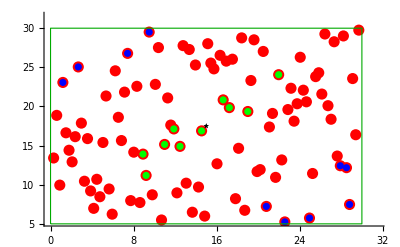
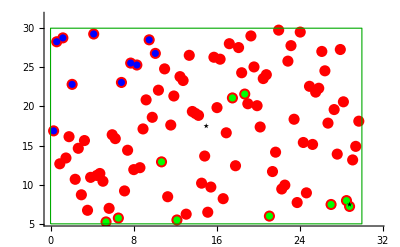
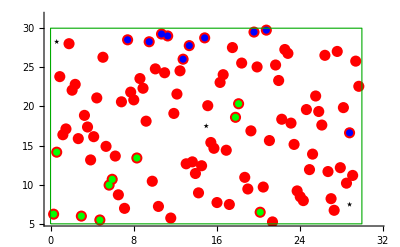
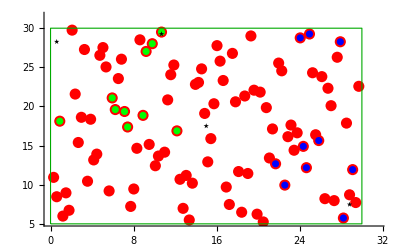
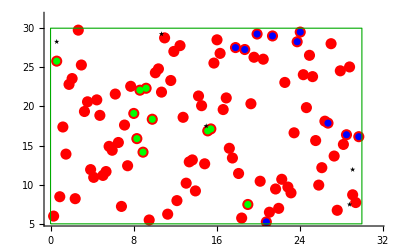
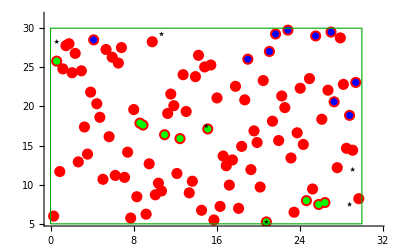
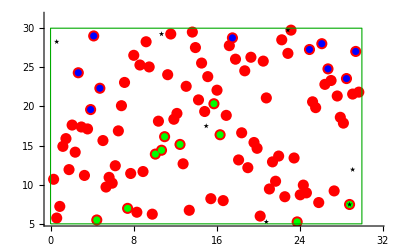
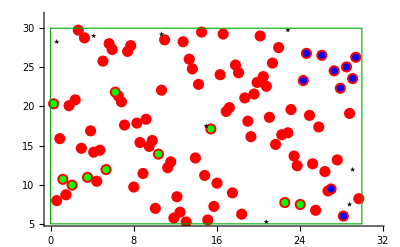

```mathematica
Plots
```

## In here we calculate the results for theSVD Basis

```mathematica
BaseSVD=SVDCreator[BasisConstruction[TotalBasisSmall],2];
```

```mathematica
Length[TotalBasisSmall]
```

20

```mathematica
BasisNoSDV=BasisConstruction[TotalBasisSmall];
```

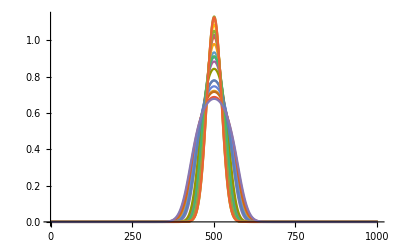

```mathematica
ListPlot[BasisNoSDV,Joined->True,PlotRange->All]
```

## Here are the final results for the table

```mathematica
Matrix2=LHCMatrixRandomizer[2]
Matrix4=LHCMatrixRandomizer[4]
Matrix8=LHCMatrixRandomizer[8]
```

{{1,1},{2,2}}

{{1,4},{2,3},{3,1},{4,2}}

{{1,5},{2,7},{3,3},{4,4},{5,6},{6,1},{7,8},{8,2}}

Lagrange basis:

```mathematica
ResL2=Timing[ResultsCalculator[SVDCreator[BasisConstruction[Matrix2],2]]]
ResL4=Timing[ResultsCalculator[SVDCreator[BasisConstruction[Matrix4],4]]]
ResL8=Timing[ResultsCalculator[SVDCreator[BasisConstruction[Matrix8],8]]]
```

{1.3131,{0.447252,0.0965332}}

{2.94162,{1.16718,0.00296146}}

{20.7245,{14.1881,0.0000133206}}

POD Greedy

```mathematica
ResPODG2=Timing[ResultsCalculator[SVDCreator[BasisConstruction[TotalBasisSmall],2]]]
```

{4.47547,{0.448461,0.0147121}}

```mathematica
ResPODG4=Timing[ResultsCalculator[SVDCreator[BasisConstruction[TotalBasisSmall],4]]]
```

{5.70722,{1.20963,0.000214117}}

```mathematica
ResPODG8=Timing[ResultsCalculator[SVDCreator[BasisConstruction[TotalBasisSmall],8]]]
```

{19.2528,{11.3469,2.03049×10^-8}}

POD alone

```mathematica
ResPOD2=Timing[ResultsCalculator[SVDCreator[BasisConstruction[TraininPointsMakerTrain[MatrixLH]],2]]]
```

{3.90535,{0.447183,0.0115169}}

```mathematica
ResPOD4=Timing[ResultsCalculator[SVDCreator[BasisConstruction[TraininPointsMakerTrain[MatrixLH]],4]]]
```

{6.05911,{1.38687,0.000558127}}

```mathematica
ResPOD8=Timing[ResultsCalculator[SVDCreator[BasisConstruction[TraininPointsMakerTrain[MatrixLH]],8]]]
```

{24.1046,{14.4726,1.71354×10^-7}}